```mathematica
SetDirectory[NotebookDirectory[]];
$PlotTheme = "Default";
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];

colorMap = 97;
thesisImages = FileNameJoin[{NotebookDirectory[],"..","..","thesis", "chapters", "img"}];

resultroot = FileNameJoin[{NotebookDirectory[], "results"}];
dataroot = FileNameJoin[{NotebookDirectory[], "data"}];
cm = 72/2.54;
Needs["ErrorBarPlots`"];
```

```mathematica
Needs["DatabaseLink`"];
<<"helpers-scores.wls";
<<"helpers-data.wls";
<<"scores.wls";
```

```mathematica
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments->"-Xmx4096m"];
conn = OpenSQLConnection[JDBC["PostgreSQL","teodor-desktop/teodor"],"Username"->"teodor", "Password"-> "4HWZQ3y60gKKcTNp"];
```

## Classify Simulated Tracks

### Read Data

```mathematica
ids = SQLExecute[conn, "select id from smidata where dataset_id in (select id from smidata_desc where description = 'Simulated positive and negative tracks for testing smi-classify')"];
```

#### Extract data set with the old level detection algorithm.

```mathematica
data = whitenData@readTracksByIds[conn,ids, levelsOldI];
```

```mathematica
Union[Head/@Flatten@Keys@data]
```

{Real}

```mathematica
N@Total[#[[1;;20]]]/Total[#] &@Eigenvalues@Covariance@Keys@data
```

0.95138

```mathematica
BinarySerialize[data]>> "data/simulated-oldlevels-raw.bin";
BinarySerialize[compressPCA[data, 20]]>> "data/simulated-oldlevels-pca20.bin"
```

#### Extract data set with the new level detection algorithm.

```mathematica
data = whitenData@readTracksByIds[conn,ids, levelsI];
```

```mathematica
Union@(Head/@Flatten@Keys@data)
```

{Real}

```mathematica
N@Total[#[[1;;20]]]/Total[#] &@Eigenvalues@Covariance@Keys@data
```

0.958329

Export the a raw data set and a compressed data set.

```mathematica
BinarySerialize[data]>> "data/simulated-newlevels-raw.bin";
BinarySerialize[compressPCA[data, 20]]>> "data/simulated-newlevels-pca20.bin"
```

```mathematica
N@Length@Select[data, Values@# ===yes&]/Length[Select[data, Values@#===no&]]
```

### Plot The Results

```mathematica
newLevelsRaw = BinaryDeserialize[<<"data/simulated-newlevels-raw.bin"];
newLevelsPCA = BinaryDeserialize[<<"data/simulated-newlevels-pca20.bin"];
oldLevelsRaw = BinaryDeserialize[<<"data/simulated-oldlevels-raw.bin"];
oldLevelsPCA = BinaryDeserialize[<< "data/simulated-oldlevels-pca20.bin"];
```

```mathematica
{Length@Select[newLevelsRaw, Values@#==yes&],Length[Select[newLevelsRaw, Values@#==no&]]}
```

{316,23148}

```mathematica
{#,N@#[[1]]/ #[[2]]}&@{Length@Select[oldLevelsRaw, Values@#==yes&],Length[Select[oldLevelsRaw, Values@#==no&]]}
```

{{316,23043},0.0137135}

```mathematica
evalsNew = Eigenvalues@Covariance@Keys@newLevelsRaw;
evalsOld = Eigenvalues@Covariance@Keys@oldLevelsRaw;
```

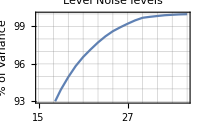
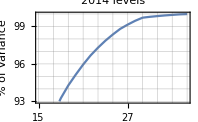

```mathematica
Block[{img}, 
img =Row[
Function[{evals, label},
ListLinePlot[{#,(Total[evals[[1;;#]]]/Total@evals * 100)}&/@ Range[15, 35],
Frame->True,
FrameTicks->{
{Range[93, 100, 1],None },
{Range[15, 35,2], None}
},
GridLines->{Range[15, 35, 2], Range[93, 100, 1]},
FrameTicksStyle->frameTicksStyle,
PlotStyle->ColorData[colorMap],
PlotRange->{{15, 35},{93, 100}},
PlotLabel->plotLabelStyle@label,
ImageSize->7cm,
FrameLabel -> (frameLabelStyle/@{"Number of PC", "% of Variance"})
]
]@@@ {{evalsNew,"Level Noise levels"},{evalsOld, "2014 levels"}}
];
Export[FileNameJoin[{thesisImages, "classify-smi-property-pca-simulated.pdf"}], img];
img]
```

```mathematica
resNewLevelsRaw = BinaryDeserialize[<<"results/simulated-newlevels-raw.bin"];
resOldLevelsRaw = BinaryDeserialize[<<"results/simulated-oldlevels-raw.bin"];
resNewLevelsPCA = BinaryDeserialize[<<"results/simulated-newlevels-pca20.bin"];
resOldLevelsPCA = BinaryDeserialize[<<"results/simulated-oldlevels-pca20.bin"];
```

```mathematica
notANumber = "nan";
```

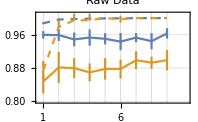
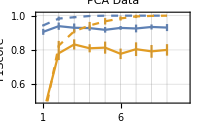

```mathematica
Block[{train, test, prepareToPlot, img},
train = 1;
test = 2;
prepareToPlot[data_, index_]:= 
Transpose[{
Transpose[{Range[1, 9],Mean[Select[#, #≠ notANumber&]]&/@Transpose[data, {3, 2, 1}][[index]]}],
ErrorBar@StandardDeviation[Select[#, #≠ notANumber&]]&/@Transpose[data, {3, 2, 1}][[index]]
}];

img = Column[{
Row[{
ErrorListPlot[{
prepareToPlot[resNewLevelsRaw, train],
prepareToPlot[resNewLevelsRaw, test],
prepareToPlot[resOldLevelsRaw, train],
prepareToPlot[resOldLevelsRaw, test]
},
PlotLabel->plotLabelStyle["Raw Data"],
Joined->True,
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
FrameTicks->{{Automatic, None}, {Range[1, 10], None}},
PlotRange->{{0.7,10.3},{0.8, 1.01}},
FrameLabel-> frameLabelStyle/@{"Hidden Units", "F1Score"},
GridLines->{Range[1, 9], Automatic},
PlotStyle-> {
{ColorData[colorMap][1], Dashed},
{ColorData[colorMap][1], Thick},
{ColorData[colorMap][2], Dashed},
{ColorData[colorMap][2], Thick}},
ImageSize->7cm
],

ErrorListPlot[{
prepareToPlot[resNewLevelsPCA, train],
prepareToPlot[resNewLevelsPCA, test],
prepareToPlot[resOldLevelsPCA, train],
prepareToPlot[resOldLevelsPCA, test]
},
PlotLabel->plotLabelStyle["PCA Data"],
Joined->True,
Frame-> True,
FrameTicksStyle-> frameTicksStyle,
FrameTicks->{{Automatic, None}, {Range[1, 10], None}},
PlotRange->{{0.7,10.3},{0.5, 1.01}},
FrameLabel-> frameLabelStyle/@{"Hidden Units", "F1Score"},
GridLines->{Range[1, 9], Automatic},
PlotStyle-> {
{ColorData[colorMap][1], Dashed},
{ColorData[colorMap][1], Thick},
{ColorData[colorMap][2], Dashed},
{ColorData[colorMap][2], Thick}},
ImageSize->7cm
]}],
LineLegend[{
{ColorData[colorMap][1], Dashed},
ColorData[colorMap][1],
{ColorData[colorMap][2],Dashed},
ColorData[colorMap][2]
},
legendStyle/@{"Levels Noise Train",
"Levels Noise Test",
"2014 levels Train",
"2014 levels Test"},
LegendLayout->"Row"]
}, Alignment->Center];
Export[FileNameJoin[{thesisImages, "classify-smi-nn-f1score-simulated.pdf"}], img];
img
]
```

```mathematica
prepareToPlot[data_, index_]:= 
Transpose[{
Transpose[{Range[1, 9],Mean[Select[#, #≠ notANumber&]]&/@Transpose[data, {3, 2, 1}][[index]]}],
ErrorBar@StandardDeviation[Select[#, #≠ notANumber&]]&/@Transpose[data, {3, 2, 1}][[index]]
}];
```

```mathematica
prepareToPlot[resNewLevelsRaw, 2]
```

{{{1,0.95975931832871586},ErrorBar[0.009028072960368238]},{{2,0.959093107339331608},ErrorBar[0.01407257436297278]},{{3,0.948807244292615448},ErrorBar[0.01645545716238018]},{{4,0.95330988144007075},ErrorBar[0.01959034399999008]},{{5,0.950329415590817528},ErrorBar[0.01347825610614366]},{{6,0.943518625836447911},ErrorBar[0.020693558034146824]},{{7,0.953153153512032703},ErrorBar[0.01090435493722863]},{{8,0.944550090424540423},ErrorBar[0.019251334186634302]},{{9,0.963190738699298898},ErrorBar[0.01244788788417929]}}

```mathematica
prepareToPlot[resOldLevelsRaw, 2]
```

{{{1,0.847428834900750744},ErrorBar[0.028596463553844893]},{{2,0.881590797575505269},ErrorBar[0.037281548639973566]},{{3,0.879653822429032251},ErrorBar[0.024016133032113567]},{{4,0.869664046626940168},ErrorBar[0.021505106930420433]},{{5,0.877840987648808324},ErrorBar[0.025662357104647066]},{{6,0.877766026561008939},ErrorBar[0.02289224584951151]},{{7,0.89876040451355258},ErrorBar[0.021347956839418266]},{{8,0.892982002503680894},ErrorBar[0.01442862082075742]},{{9,0.898962065430680224},ErrorBar[0.02461018622321354]}}

```mathematica
prepareToPlot[resNewLevelsPCA, 2]
```

{{{1,0.905637272207902815},ErrorBar[0.017351053792980318]},{{2,0.938740680356702595},ErrorBar[0.021194663088803318]},{{3,0.929462017857038958},ErrorBar[0.024757631348257501]},{{4,0.927363694191443133},ErrorBar[0.01520801136079572]},{{5,0.917364296162391357},ErrorBar[0.01636019604263041]},{{6,0.928539495371479962},ErrorBar[0.01113082944643961]},{{7,0.925179154397230041},ErrorBar[0.022674466715404556]},{{8,0.934103960162348945},ErrorBar[0.01463415004144505]},{{9,0.930526169331939157},ErrorBar[0.020507171934230193]}}

```mathematica
prepareToPlot[resOldLevelsPCA, 2]
```

{{{1,0.42934029733372205},ErrorBar[0.040488321253172165]},{{2,0.780492649480679734},ErrorBar[0.039758317379278773]},{{3,0.832034264505619214},ErrorBar[0.029668136824597334]},{{4,0.809635305493186086},ErrorBar[0.023611371263139087]},{{5,0.813390613831578702},ErrorBar[0.035165106228600694]},{{6,0.777353228519890094},ErrorBar[0.030523008084266847]},{{7,0.804353541237399639},ErrorBar[0.039926979559976612]},{{8,0.791607551422999323},ErrorBar[0.037117087133981597]},{{9,0.800199390662796906},ErrorBar[0.033521699130756033]}}

## Classify Manual Selections

### Read Data

```mathematica
ids = SQLExecute[conn, "select id from smidata where dataset_id in (select id from smidata_desc where description = 'Manually selected tracks') and lda_filter > 0.01"];
```

#### Extract data with old LD algorithm.

```mathematica
data = readTracksByIds[conn, ids, levelsOldI];
```

```mathematica
BinarySerialize[data]>>"data/manual-oldlevels-dirty-raw.bin"
```

```mathematica
data = BinaryDeserialize[<<"data/manual-oldlevels-dirty-raw.bin"];
```

```mathematica
Union@(Head/@Flatten@Keys@data)
```

{Real,Symbol}

```mathematica
cleanData = whitenData@Select[data, Union[Head/@Keys@# ] === {Real}&];
```

```mathematica
Union@(Head/@Flatten@Keys@cleanData)
```

{Real}

```mathematica
BinarySerialize[cleanData]>> "data/manual-oldlevels-raw.bin"
```

```mathematica
ev = Eigenvalues@Covariance@Keys@cleanData;
```

```mathematica
Total[ev[[1;;26]]]/Total[ev]
```

0.959436

```mathematica
BinarySerialize[compressPCA[cleanData, 26]]>>"data/manual-oldlevels-pca26.bin"
```

#### Extract data with new LD algorithm.

```mathematica
data = readTracksByIds[conn, ids, levelsI];
```

```mathematica
BinarySerialize[data]>>"data/manual-newlevels-dirty-raw.bin"
```

```mathematica
data = BinaryDeserialize[<<"data/manual-newlevels-dirty-raw.bin"];
```

```mathematica
Union@(Head/@Flatten@Keys@data)
```

{Real,Symbol}

```mathematica
cleanData = whitenData@Select[data, Union[Head/@Keys@# ] === {Real}&];
```

```mathematica
Union@(Head/@Flatten@Keys@cleanData)
```

{Real}

```mathematica
BinarySerialize[cleanData]>> "data/manual-newlevels-raw.bin"
```

```mathematica
ev = Eigenvalues@Covariance@Keys@cleanData;
```

```mathematica
Total[ev[[1;;26]]]/Total[ev]
```

0.955718

```mathematica
BinarySerialize[compressPCA[cleanData, 26]]>>"data/manual-newlevels-pca26.bin"
```

### Plot The Results

```mathematica
newLevelRaw = BinaryDeserialize[<<"data/manual-newlevels-raw.bin"];
oldLevelRaw = BinaryDeserialize[<<"data/manual-oldlevels-raw.bin"];
```

```mathematica
{Length@Select[newLevelRaw, Values@#==yes&], Length@Select[newLevelRaw, Values@#==no&]}
```

{3431,247196}

```mathematica
{Length@Select[oldLevelRaw, Values@#==yes&], Length@Select[oldLevelRaw, Values@#==no&]}
```

{3379,231595}

```mathematica
evalsNew = Eigenvalues@Covariance@Keys@newLevelRaw;
evalsOld = Eigenvalues@Covariance@Keys@oldLevelRaw;
```

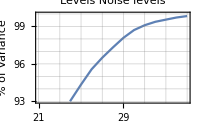
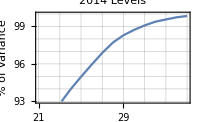

```mathematica
Block[{img}, 
img =Row[
Function[{evals, label},
ListLinePlot[{#,(Total[evals[[1;;#]]]/Total@evals * 100)}&/@ Range[21, 35],
Frame->True,
FrameTicks->{
{Range[93, 100, 1],None },
{Range[21, 35,2], None}
},
GridLines->{Range[21, 35, 2], Range[93, 100, 1]},
FrameTicksStyle->frameTicksStyle,
PlotStyle->ColorData[colorMap],
PlotRange->{{21, 35},{93, 100}},
PlotLabel->plotLabelStyle@label,
ImageSize->7cm,
FrameLabel -> (frameLabelStyle/@{"Number of PC", "% of Variance"})
]
]@@@ {{evalsNew,"Levels Noise levels"},{evalsOld, "2014 Levels"}}
];
Export[FileNameJoin[{thesisImages, "classify-smi-property-pca-manual.pdf"}], img];
img]
```

## Manual Track Inspection

```mathematica
dirty = Keys@Select[BinaryDeserialize[<<"data/manual-newlevels-dirty-raw.bin"], Values@#==yes&];
```

```mathematica
goesToZero = dirty[[All, 17]];
stepRatio = dirty[[All, 16]];
```

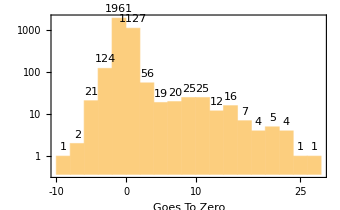

```mathematica
Block[{img},
img = Histogram[
goesToZero,20,
"LogCount", LabelingFunction->Above,
PlotRange->All,
FrameTicks->{{-10,-5,-2, 0,2, 5, 10, 15, 20, 25}, Automatic},
FrameTicksStyle->frameTicksStyle,
Frame-> True,
FrameLabel->{frameLabelStyle@"Goes To Zero", None},
ImageSize->12cm
];
Export[FileNameJoin[{thesisImages, "classify-smi-mistake-goes-to-zero.pdf"}], img];
img
]
```

```mathematica
Length@Select[goesToZero, #< -2 || #> 2&]
```

343

```mathematica
N@Length@Select[goesToZero, #< -2 || #> 2&]/Length@goesToZero
```

0.0999709

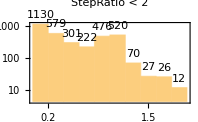
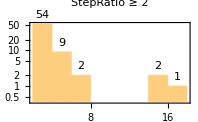

```mathematica
Block[{img},
img = Row[{
Histogram[
Select[stepRatio, #<2&],
10,"LogCount",LabelingFunction->Above,
FrameTicks->{ {Automatic, None}, {{0.2, 0.5, 1.0, 1.5, 2.0}, None}},
FrameTicksStyle-> frameTicksStyle,
Frame-> True,
ImageSize->7cm,
PlotRange->All,
FrameLabel->{frameLabelStyle@"Step Ratio",None}, 
PlotLabel->plotLabelStyle@"StepRatio < 2"],
Histogram[
Select[stepRatio, #≥2&],
10,"LogCount",LabelingFunction->Above,
FrameTicks->{Automatic, Automatic},
FrameTicksStyle-> frameTicksStyle,
Frame-> True,
ImageSize->7cm,
PlotRange->All,
FrameLabel->{frameLabelStyle@"Step Ratio",None},
PlotLabel->plotLabelStyle@"StepRatio ≥ 2"]
}];
Export[FileNameJoin[{thesisImages, "classify-smi-mistake-stepratio.pdf"}], img];
img]
```

```mathematica
{Length@Select[stepRatio, #> 0.2&], N@Length@Select[stepRatio, #> 0.2&]/Length@stepRatio}
```

{2301,0.67065}

```mathematica
{Length@Select[stepRatio, #> 0.3&], N@Length@Select[stepRatio, #> 0.3&]/Length@stepRatio}
```

{1959,0.570971}